```mathematica
SetDirectory[NotebookDirectory[]];

a=Sound[SoundNote["C"]];

b= AudioLocalMeasurements[a, {"SpectralRollOff"}]
```

TimeSeries[…]

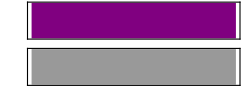

```mathematica
a
```

```mathematica
Median[b]
```

527.563

```mathematica
(*Valore atteso: 524, buon risultato*)
```

```mathematica
chiave = Import["../immagini/chiave.png"]
```

-Graphics-

```mathematica
nota = Import["../immagini/nota_senza_barra.png"]
```

-Graphics-

```mathematica
ImageCompose[chiave, nota, {300, 447}]
(*397 -> sol 
12.75 ogni nota
   409.5 -> la
422 -> si 

CIRCA 12.75 ogni nota

ecc...*)
```

-Graphics-